# Just for testing

## Initialization

```mathematica
Quit[];
```

### Start Notation to create symbols

```mathematica
Needs["Notation`"];
```

```mathematica
Symbolize[Subscript[k, max]]; (* Sumatory Maximun value *)
```

```mathematica
Symbolize[Subscript[k, B]]; (* Boltzmann's Constant *)
Symbolize[ℏ]; (* Planck's Constant *)

SetAttributes[{Subscript[k, B],ℏ,g,m},Constant]
```

### Using ‘Quantity’ to load our values in to simbolic constants

```mathematica
any = Quantity[1,"Joules"/"Kelvins"]
```

1

```mathematica
QuantityMagnitude[Quantity["BoltzmannConstant"]]
QuantityUnit[Quantity["BoltzmannConstant"]]
UnitConvert[Quantity["BoltzmannConstant"]]
```

1

BoltzmannConstant

1.3806×10^-23

```mathematica
Subscript[k, B]= Quantity["BoltzmannConstant"]/Quantity[1,"Joules"/"Kelvins"]
```

1.3806×10^-23

```mathematica
(* PlanckConstantReduced = PlanckContant / 2π *)
```

```mathematica
UnitConvert[Quantity["PlanckConstant"]]/(2π)
```

1.054572×10^-34

```mathematica
ℏ = Quantity["PlanckConstant"]/Quantity[2π,"Joules"*"Seconds"]
```

1.054572×10^-34

```mathematica
g = 9.81;
m = 1;
```

## Rules for changing variables

```mathematica
AtoB = {A-> Subscript[k, B]/2 B, c-> 1/2 B}
```

{A→6.9032×10^-24 B,c→B/2}

```mathematica
myVariable = A^2  c /. AtoB
```

2.3827×10^-47 B^3

## Rules for integration and derivation of key functions

```mathematica
1/Gamma[ν] Integrate[x^(ν-1)/(z^-1 Exp[x]+1),{x,0,∞},Assumptions->Re[ν]>0]
 1/Gamma[ν] Integrate[x^(ν-1)/(z^-1 Exp[x]-1),{x,0,∞},Assumptions->Re[ν]>0]
```

-PolyLog[ν,-z]

PolyLog[ν,z]

```mathematica
fermi[ν_,z_]:=- PolyLog[ν,-z]
bose[ν_,z_]:=PolyLog[ν,z]
```

```mathematica
Table[fermi[ν,z],{ν,1/2,3,1/2}] 
Table[bose[ν,z],{ν,1/2,3,1/2}]
```

{-PolyLog[1/2,-z],Log[1+z],-PolyLog[3/2,-z],-PolyLog[2,-z],-PolyLog[5/2,-z],-PolyLog[3,-z]}

{PolyLog[1/2,z],-Log[1-z],PolyLog[3/2,z],PolyLog[2,z],PolyLog[5/2,z],PolyLog[3,z]}

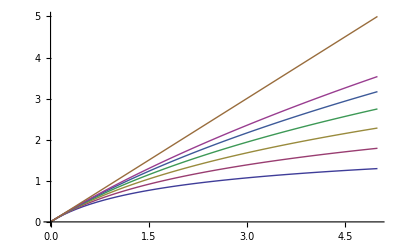

```mathematica
Plot[Evaluate[{Table[fermi[ν,z],{ν,1/2,3,1/2}],z}],{z,0,5}]
```

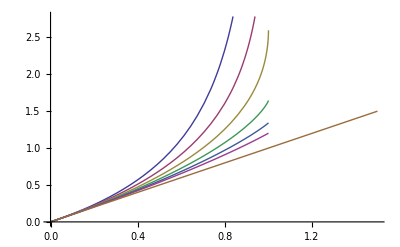

```mathematica
Plot[Evaluate[{Table[bose[ν,z],{ν,1/2,3,1/2}],z}],{z,0,1.5}]
```

Observe that our bose function cannot becomes greater that z = 1

### Series Expasion

```mathematica
Series[fermi[ν,z],{z,0,5}]
```

z-2^-ν z^2+3^-ν z^3-4^-ν z^4+5^-ν z^5+O[z]^6

This result suggest that for small values of:

```mathematica
fermiExpansion[ν_,z_,Subscript[k, max]:_]:=-∑_(k=1)^Subscript[k, max] (-z)^k/k^ν
```

Here I' m ploting fermi function for  a values of  0 < z < 1,

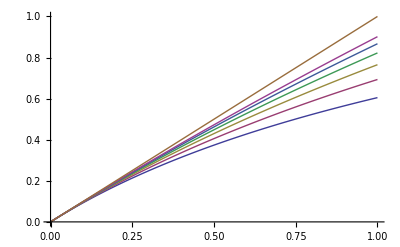

```mathematica
Plot[Evaluate[{Table[fermi[ν,z],{ν,1/2,3,1/2}],z}],{z,0,1}]
```

Testing our series expansion:

```mathematica
fermi[1,0.49] //N
```

0.398776

```mathematica
fermiExpansion[1,0.49,100] //N
```

0.398776

```mathematica
(* Notice that this approximation only works well for values below z ≈ 0.5 otherewize our numerical approximation fails to approximate our integral function, we also have assumed that ν = 1. *)
```

```mathematica
Series[bose[ν,z],{z,0,5}]
```

z+2^-ν z^2+3^-ν z^3+4^-ν z^4+5^-ν z^5+O[z]^6

This result suggest that for small values of :

```mathematica
boseExpansion[ν_,z_,Subscript[k, max]:_] := ∑_(k=1)^Subscript[k, max] z^k/k^ν
```

```mathematica
bose[1,0.89]//N
```

2.20727

```mathematica
boseExpansion[1,0.89,100]
```

2.20727

```mathematica
(* Note that our numerical approximation for bose-einstein integral stars failing for z ≈ 0.9, and assuming that ν = 1. *)
```

### Derivation

For fermi

```mathematica
D[fermi[ν,z], z]
```

-PolyLog[-1+ν,-z]/z

Thus, we rely on the PolyLog fucntions derivates, this is e

```mathematica
Dfermi[ν_,z_]:=1/z fermi[ν-1,z]
```

```mathematica
D[fermi[ν,z], z] == 1/z fermi[ν-1,z]
```

True

Similarly for bose

```mathematica
D[bose[ν,z], z]
```

PolyLog[-1+ν,z]/z

```mathematica
Dbose[ν_,z_]:=1/z bose[ν-1,z]
```

```mathematica
D[bose[ν,z], z] == Dbose[ν,z]
```

True

### Integration

Mathematica fails to recognize many of the simple variants of fermi - diract and bose - einstein integrals, therefore we need to supply extra rules to make our task easier to handle.